```mathematica
i="1"
```

1

```mathematica
X=ReadList["/home/andrey/CLionProjects/NumericalMethods/Lab5/files/X.txt",Number];
Y=Read["/home/andrey/CLionProjects/NumericalMethods/Lab5/files/Y.txt",Number];
Val=Read["/home/andrey/CLionProjects/NumericalMethods/Lab5/files/Val.txt",Number];
```

```mathematica
Val
X
Y
```

```mathematica
6.13
```

-10

-10

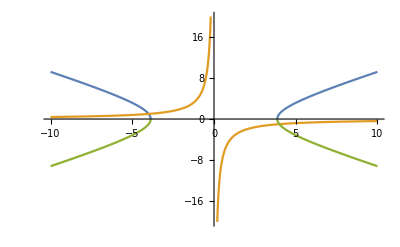

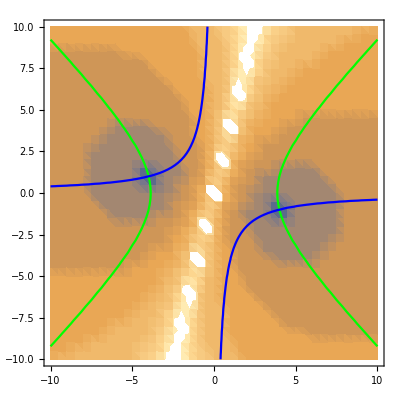

```mathematica
Plot[{Sqrt[x*x-15],-4/x,-Sqrt[x*x-15]},{x,-10,10}]

r={X,Y,Val};
r=ReadList["/home/andrey/CLionProjects/NumericalMethods/Lab5/files/Val.txt",{Number,Number,Number}];
Show[ListDensityPlot[r,Mesh->0,MeshFunctions->{Function[{x,y},Sqrt[x*x-15]],Function[{x,y,z},x*y+4]},MeshStyle->{Lighter[Red],Lighter[Green]}],ContourPlot[x1^2-x2^2-15==0,{x1,-10,10},{x2,-10,10},ContourStyle->Green],ContourPlot[x1 x2+4==0,{x1,-10,10},{x2,-10,10},ContourStyle->Blue]]
```

```mathematica
Export["/home/andrey/Рабочий стол/Методы вычислений/отчеты/Lab5/Analyt1.jpg",%180,"JPEG"]
```

/home/andrey/Рабочий стол/Методы вычислений/отчеты/Lab5/Analyt1.jpg

```mathematica
Export["/home/andrey/Рабочий стол/Методы вычислений/отчеты/Lab5/Num1.jpg",%176,"JPEG"]
```

/home/andrey/Рабочий стол/Методы вычислений/отчеты/Lab5/Num1.jpg

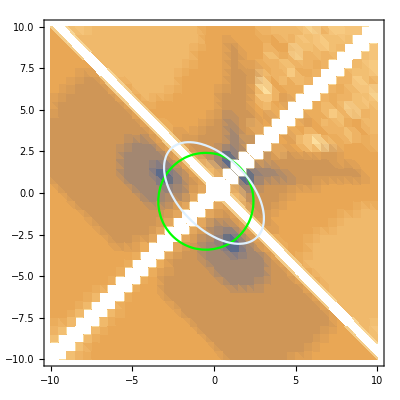

```mathematica
r=ReadList["/home/andrey/CLionProjects/NumericalMethods/Lab5/files/Val.txt",{Number,Number,Number}];
Show[ListDensityPlot[r,Mesh->0,MeshFunctions->{Function[{x,y,z},x*x+y*y+x+y-8],Function[{x,y,z},x*x+y*y+x*y-7]},MeshStyle->{Lighter[Red],Lighter[Green]}],ContourPlot[x1^2+x2^2+x1+x2-8==0,{x1,-10,10},{x2,-10,10},ContourStyle->Green],ContourPlot[x1 x2+x1^2+x2^2-7==0,{x1,-10,10},{x2,-10,10},ContourStyle->LightBlue]]
```

```mathematica
Export["/home/andrey/Рабочий стол/Методы вычислений/отчеты/Lab5/Analyt2.jpg",%183,"JPEG"]
```

/home/andrey/Рабочий стол/Методы вычислений/отчеты/Lab5/Analyt2.jpg

```mathematica
Export["/home/andrey/Рабочий стол/Методы вычислений/отчеты/Lab5/Num2.jpg",%166,"JPEG"]
```

/home/andrey/Рабочий стол/Методы вычислений/отчеты/Lab5/Num2.jpg

```mathematica
Export["/home/andrey/Рабочий стол/Методы вычислений/отчеты/Lab5/Num1.jpg",%242,"JPEG"]
```

/home/andrey/Рабочий стол/Методы вычислений/отчеты/Lab5/Num1.jpg

```mathematica
Export["/home/andrey/Рабочий стол/Методы вычислений/отчеты/Lab5/Analyt1.jpg",%235,"JPEG"]
```

/home/andrey/Рабочий стол/Методы вычислений/отчеты/Lab5/Analyt1.jpg

```mathematica
Export["/home/andrey/Рабочий стол/Методы вычислений/отчеты/Lab5/Analyt1.jpg",%210,"JPEG"]
```

/home/andrey/Рабочий стол/Методы вычислений/отчеты/Lab5/Analyt1.jpg

```mathematica
Export["/home/andrey/Рабочий стол/Методы вычислений/отчеты/Lab5/Num2.jpg",%200,"JPEG"]
```

/home/andrey/Рабочий стол/Методы вычислений/отчеты/Lab5/Num2.jpg

```mathematica
Export["/home/andrey/Рабочий стол/Методы вычислений/отчеты/Lab5/Analyt2.jpg",%193,"JPEG"]
```

/home/andrey/Рабочий стол/Методы вычислений/отчеты/Lab5/Analyt2.jpg

```mathematica
Export["/home/andrey/Рабочий стол/Методы вычислений/отчеты/Lab5/Num2.jpg",%168,"JPEG"]
```

/home/andrey/Рабочий стол/Методы вычислений/отчеты/Lab5/Num2.jpg

```mathematica
Export["/home/andrey/Рабочий стол/Методы вычислений/отчеты/Lab5/Num1.jpg",%164,"JPEG"]
```

/home/andrey/Рабочий стол/Методы вычислений/отчеты/Lab5/Num1.jpg

```mathematica
Export["/home/andrey/Рабочий стол/Методы вычислений/отчеты/Lab5/Analyt1.jpg",%160,"JPEG"]
```

/home/andrey/Рабочий стол/Методы вычислений/отчеты/Lab5/Analyt1.jpg

```mathematica
Export["/home/andrey/Рабочий стол/Методы вычислений/отчеты/Lab5/Analyt1.jpg",%153,"JPEG"]
```

/home/andrey/Рабочий стол/Методы вычислений/отчеты/Lab5/Analyt1.jpg

```mathematica
|
```

```mathematica
ListDensityPlot[{{0,0,1},{1,0,0},{0,1,0}},Mesh->All]


dataApproxLU = Import[fileApproxLU,"CSV"];
dataApproxLC = Import[fileApproxLC,"CSV"];
dataApproxCUB = Import[fileApproxCUB,"CSV"];
dataAccurLU = Import[fileAccurLU,"CSV"];
dataAccurLC = Import[fileAccurLC,"CSV"];
dataAccurCUB = Import[fileAccurCUB,"CSV"];
```

-Graphics-

Import::chtype: First argument fileApproxLU is not a valid file, directory, or URL specification.

Import::chtype: First argument fileApproxLC is not a valid file, directory, or URL specification.

Import::chtype: First argument fileApproxCUB is not a valid file, directory, or URL specification.

Import::chtype: First argument fileAccurLU is not a valid file, directory, or URL specification.

Import::chtype: First argument fileAccurLC is not a valid file, directory, or URL specification.

Import::chtype: First argument fileAccurCUB is not a valid file, directory, or URL specification.

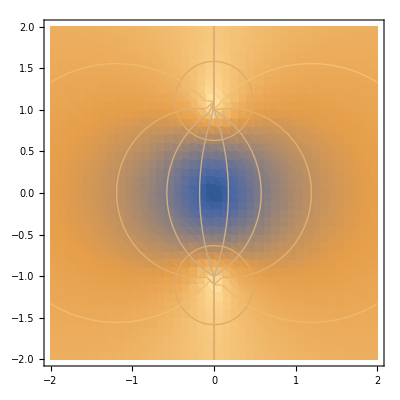

```mathematica
data=Flatten[Table[{x,y,Abs[ArcTan[x+I y]]},{x,-2,2,0.1},{y,-2,2,0.1}],1];
ListDensityPlot[data,Mesh->8,MeshFunctions->{Function[{x,y,z},Re[ArcTan[x+I y]]],Function[{x,y,z},Im[ArcTan[x+I y]]]},MeshStyle->{Lighter[Red],Lighter[Green]}]
```

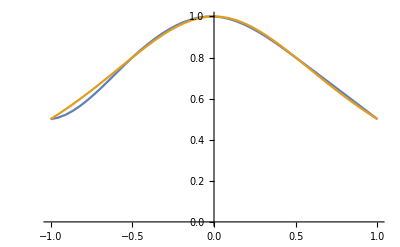

```mathematica
ListLinePlot[{dataApproxCUB,dataAccurLU}]
```

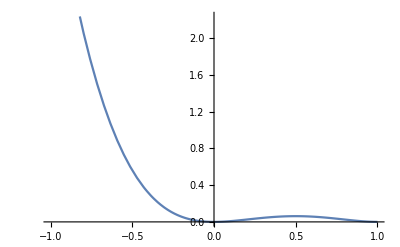

```mathematica
Plot[(x-1)^2*x*x,{x,-1,1}]
```

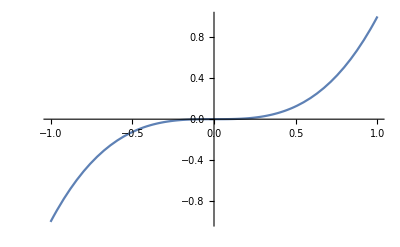

Plot::pllim: Range specification {x,-1,0,1} is not of the form {x, xmin, xmax}.

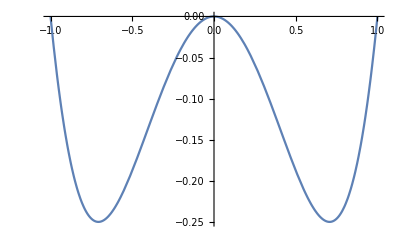

```mathematica
Plot[x*x*x,{x,-1,1}]
```